## Turing Machine 5 States 3 Colors

### Basic Information

For every pair of states and colors, the Turing machine rule picks a new state of the Turing machine, and a new color for the active cell, and a direction either left and right for the active cell to move.  The active cell is usually called the head of the Turing machine.

For 3 states and 5 colors there are 15 pairs, and for each of those pairs there are 30 possible choices.
So there are 30^15 = 14348907000000000000000 possible Turing machines.

#### Evaluate a TM

```mathematica
$MaxRules=30^15;
```

```mathematica
$Steps=500;
```

```mathematica
$SampleSize= 10000;
```

```mathematica
TM[rn_]:= TuringMachine[{rn,5,3},{1,{{1,0,1},0}},$Steps]
```

```mathematica
BigTM[rn_,steps_]:=TuringMachine[{rn,5,3},{1,{{1,0,1},0}},steps]
```

#### Show a TM

```mathematica
ShowTM[rn_]:= ArrayPlot[Last/@ TM[rn],ImageSize->{500,500},PlotLabel->rn,ColorFunction->"Rainbow"] (* standard size $Steps *)
```

```mathematica
ShowBigTM[rn_,steps_]:=ArrayPlot[Last/@ BigTM[rn,steps],ImageSize->{Automatic,500},PlotLabel->rn]
```

```mathematica
ShowTMwithHead[rn_]:= 
		ArrayPlot[
			Function[u,MapAt[Red&,u[[2]],u[[1,2]]]] /@ 
				TM[rn],ImageSize->{Automatic,500},PlotLabel->rn] (* standard size $Steps *)
```

```mathematica
ShowHorizontalTM[rn_,steps_,extraopts___]:=ArrayPlot[Reverse[Transpose[Last/@ BigTM[rn,steps]]],
	extraopts,ImageSize->{800,200},ColorFunction->"Rainbow"]
```

```mathematica
ShowDivededTM[tm_,rn_,windows_]:=
With[{portion=N[Length[tm]/windows]},
	Do[
		ArrayPlot[
			Function[u,MapAt[Red&,u[[2]],u[[1,2]]]] /@ tm[[Round[i*portion];;Round[(portion+i*portion)-1]]]
			,
            ImageSize->{Automatic,500},PlotLabel->rn
		]
		
	,{i,0,windows}]
]
```

### How to find some interesting TMs

#### Criteria based on Width

```mathematica
MaxWidth[tm_]:=With[
	{relativepos=tm[[All,1,3]]}, 
	left=Select[relativepos,Positive];
	right=Select[relativepos,Negative];
	If[Length[left]>0,Max[left],0.]-If[Length[right]>0,Min[right],0.]
]
```

```mathematica
MaxWidthCriterion[tm_,rn_]:=If[(MaxWidth[tm]<(Length[tm]/3))&&(MaxWidth[tm]>10),rn,"NotInteresting"]
```

```mathematica
ApplyCriterionAndPrint[criterion_,samplesize_]:=(
	SetDirectory["/Users/Levantina/Documents/WOLFRAM/Homework2013"];
		Do[
			(r=RandomInteger[$MaxRules-1];
			max=criterion[TM[r],r];
			If[max≠"NotInteresting",(max>>> goodWidthTM.txt),""])
				
			,
		{i,samplesize}];SetDirectory[];)
```

```mathematica
ApplyCriterionAndPrint[MaxWidthCriterion,1000]
```

#### Criteria based on Entropy

```mathematica
FirstCriterion[tm_,rn_]:= With[
	{heads= tm[[All,1,3]]},
		If[Length[Tally[Partition[Differences[heads],4,1]]]>5,rn,"NotInteresting"]]
```

```mathematica
SecondCriterion[tm_,rn_]:= With[
	{heads= tm[[All,1,3]]},
		If[N[Entropy[Partition[Differences[heads],8,1]]]>2,rn,"NotInteresting"]]
```

```mathematica
Sample[size_]:= RandomInteger[$MaxRules-1,size]
```

```mathematica
ApplyOnSample[criterion_,rules_]:= DeleteCases[criterion[#]& /@ rules,"NotInteresting"]
```

```mathematica
ApplyOnSample2[criterion_,rules_]:= DeleteCases[criterion[TM[#],#]& /@ rules,"NotInteresting"]
```

```mathematica
PLogP[x_]:=-Total[x * Log[N[x]]];
TrailEntropy[pos_]:=PLogP @ Normalize[Tally[Partition[Differences[pos],8,1]][[All, 2]], Total];
```

```mathematica
RuleEntropy[rn_]:=TrailEntropy[TM[rn][[50;; , 1,2]]];
```

```mathematica
FindMaxEntropy[rules_,entropies_]:= With[{max= Max[entropies]},rules[[Flatten[Position[entropies,max],2]]]]
```

```mathematica
rules= RandomInteger[$MaxRules-1,$SampleSize];
```

```mathematica
entropies= Map[RuleEntropy[#]&, rules];
```

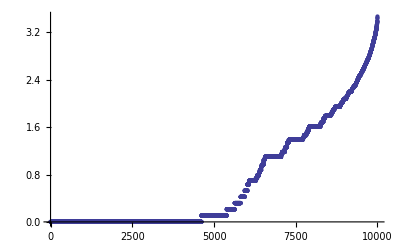

```mathematica
ListPlot[Sort[entropies]]
```

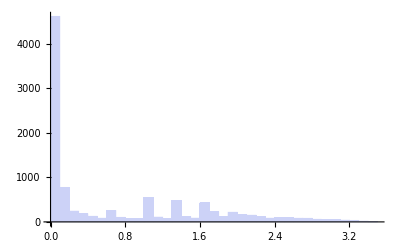

```mathematica
Histogram[entropies]
```

### Apply Entropy Criterion to a Set of Samples

```mathematica
ExploreEntropies[samplesize_,numberofsamples_]:= Do[
	r=Sample[samplesize];
	Print @ FindMaxEntropy[r,Map[RuleEntropy[#]& ,r]]
	,
	{i,numberofsamples}]
```

```mathematica
ExploreEntropies2[samplesize_,numberofsamples_]:= 
	(SetDirectory["/Users/Levantina/Documents/WOLFRAM/Homework2013"];
		Do[
			r=Sample[samplesize];
			FindMaxEntropy[r,Map[RuleEntropy[#]& ,r]] >>> goodTM.txt
			,
		{i,numberofsamples}];SetDirectory[];)
(* this prints the results step by step in a file *)
```

```mathematica
(*On a sample of 10000 rules this function is going to find the most entropic rule, and it repeat that 100 times. The TM are of 500 steps. *)
```

```mathematica
ExploreEntropies2[500,100]
```

### How widths are distributed in a random sample of 10^4 TM

```mathematica
Width[rules_]:=(SetDirectory["/Users/Levantina/Documents/WOLFRAM/Homework2013"];
		rn=0;
		Do[rn=rules[[i]];
		mytm=TM[rn];
		mov=RelativeAverageHeadMovements[mytm];
			Abs[(mov[[2]]-mov[[1]])/Length[mytm]]>>> widthsTM.txt
			,
		{i,Length[rules]}];SetDirectory[];) (* I decidet to divide to the number of the steps *)
```

```mathematica
WidthDistribution[list_,Size_]:= (
	h=Tally[N[Round[1000 #]/1000]& /@ list];
	{#,N[(#2/Size)]}& @@@ h)
```

```mathematica
Width[Sample[10000]]
```

```mathematica
SetDirectory["/Users/Levantina/Documents/WOLFRAM/Homework2013"];
```

```mathematica
l=ReadList["widthsTM.txt",Real];
```

```mathematica
SetDirectory[];
```

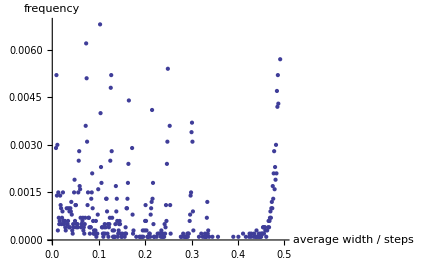

```mathematica
ListPlot[WidthDistribution[l,10000],AxesLabel->{"average width / steps","frequency"}]
```

### My favorite Turing Machine 5 States 3 Colors

#### Endurance

The Turing Machine with the rule 4842025660255448110039 attracted my attention, it has a semi-periodic behaviour, and its period grows in time, and the thing that more interested me was that it can survive without transition at least 10 000 time steps. To study the sample I used primarily a criterion based on Entropy. I wrote also a criterion based on the average width of the TMs, that helps to exclude the trivial Turing Machines; if they have a too large width it means that they evolve almost constantly in the same direction, and with a too small widht they don’t evolve enough to have an interesting behaviour. To find this TM I analyzed a sample of 10 000 TM, evolving for 500 steps, and I selected the one with the largest entropy. I did this selection for 500 times. Plotting the Turing Machines I found some interesting behaviours, but increasing the number of steps often they weren’t interesting anymore. I did a plot of 10 000 steps and I heard the sound due to the movement of the head for 100 000 steps.

```mathematica
ListPlay[BigTM[4842025660255448110039,100000][[All,1,2]],SampleRate->1760]
```

-Graphics-

```mathematica
ShowHorizontalTM[4842025660255448110039,10000,PlotLabel->4842025660255448110039,ImageSize->2000,Frame->False,PlotRangePadding->0]
```

-Graphics-

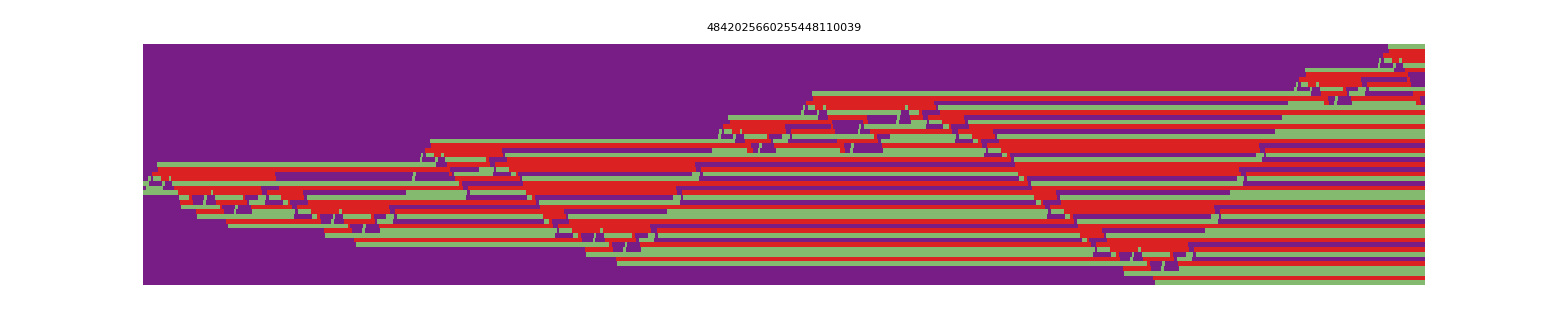

```mathematica
ShowHorizontalTM[4842025660255448110039,1000,PlotLabel->4842025660255448110039,ImageSize->1000,Frame->False,PlotRangePadding->0]
```

```mathematica
tmm=BigTM[4842025660255448110039,10000]
```

{{{1,56,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},«9999»,{{4,168,112},{1,2,1,1,2,0,1,2,0,2,1,1,«149»,1,2,1,1,2,1,0,2,2,2,1}}}

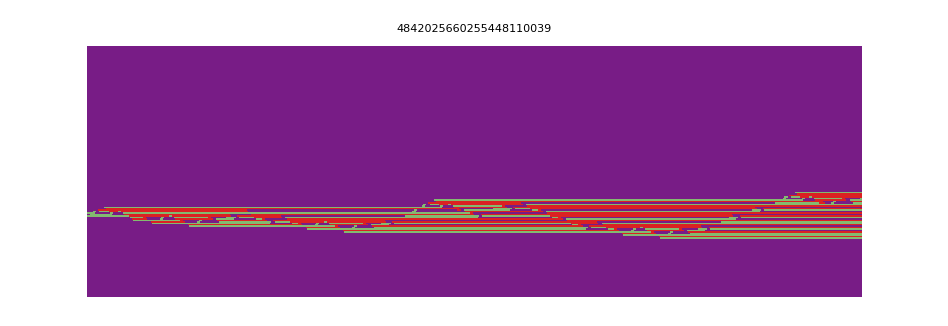

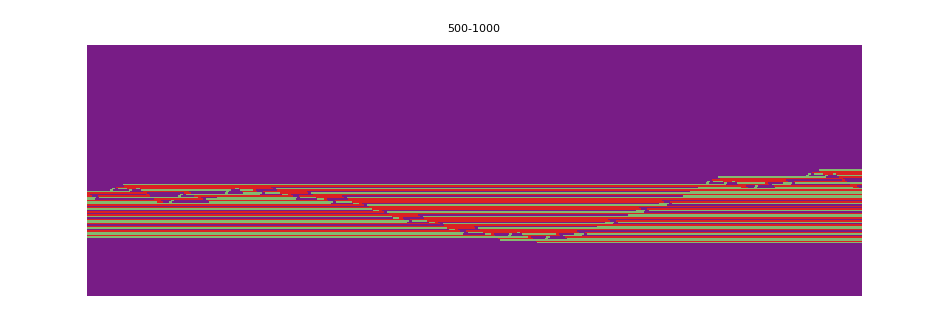

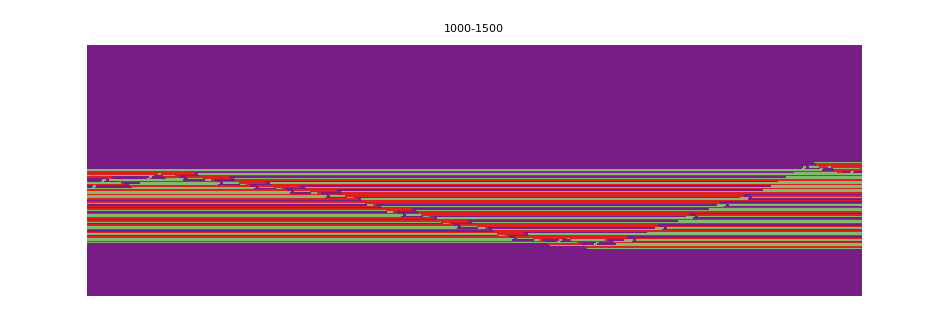

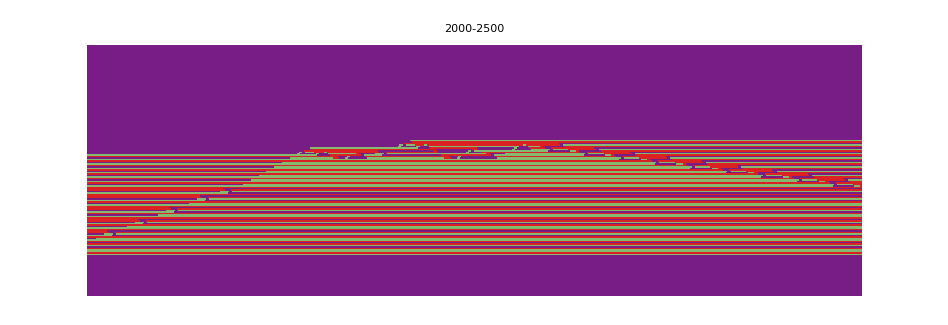

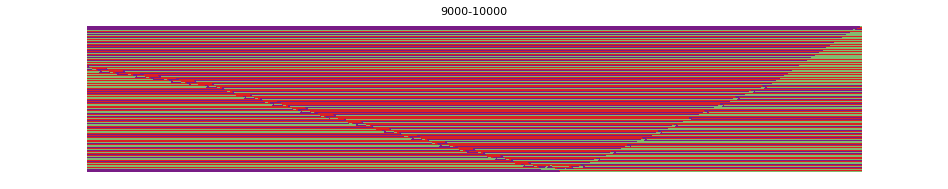

```mathematica
ArrayPlot[Reverse[Transpose[Last/@ tmm[[1;;500]]]],PlotLabel->4842025660255448110039,Frame->False,PlotRangePadding->0,ColorFunction->"Rainbow"]
ArrayPlot[Reverse[Transpose[Last/@ tmm[[500;;1000]]]],PlotLabel->"500-1000",Frame->False,PlotRangePadding->0,ColorFunction->"Rainbow"]
ArrayPlot[Reverse[Transpose[Last/@ tmm[[1000;;1500]]]],PlotLabel->"1000-1500",Frame->False,PlotRangePadding->0,ColorFunction->"Rainbow"]
ArrayPlot[Reverse[Transpose[Last/@ tmm[[2000;;2500]]]],PlotLabel->"2000-2500",Frame->False,PlotRangePadding->0,ColorFunction->"Rainbow"]
ArrayPlot[Reverse[Transpose[Last/@ tmm[[9000;;10000]]]],PlotLabel->"9000-10000",Frame->False,PlotRangePadding->0,ColorFunction->"Rainbow"]
```